# Coin Tossing

{0,0.1,0.3,0.3,0.23,0.03}

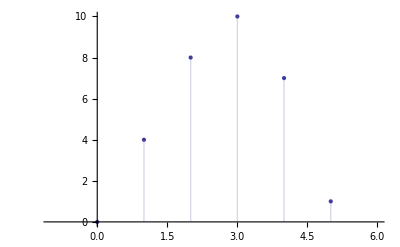

```mathematica
m=30; (* # of round *)
n=5; (* # of toss *)
A=Table[Table[Random[Integer,{0,1}],{i,1,n}],{j,1,m}];
N0=Table[Count[A[[j]],0],{j,1,m}]; (*number of "0" in A*)
N1=Table[Count[A[[j]],1],{j,1,m}] ;
B=Table[{i,Count[N0,i]},{i,0,n}];
MB=Max[Table[Count[N0,i],{i,0,n+1}]];
P=N[Table[B[[i]][[2]],{i,1,n+1}]/m,2]
ListPlot[B,PlotRange->{{-1,n+1},{0,MB}},Filling->Axis,Axes->{True,False}]
```